```mathematica
Table[∑_(k=1)^n 1/2^k, {n, 1, 10}]
```

{1/2,3/4,7/8,15/16,31/32,63/64,127/128,255/256,511/512,1023/1024}

```mathematica
Table[(2^m-1)/2^m, {m, 1, 10}]
```

{1/2,3/4,7/8,15/16,31/32,63/64,127/128,255/256,511/512,1023/1024}

```mathematica
Table[1-1/2^m, {m, 1, 10}]
```

{1/2,3/4,7/8,15/16,31/32,63/64,127/128,255/256,511/512,1023/1024}

```mathematica
Limit[∑_(k=1)^n 1/2^k, n-> ∞]
```

1

```mathematica
Apart[1/(m(m+3))]
```

1/(3 m)-1/(3 (3+m))

```mathematica
Sn[n_]:=Piecewise[{{1/(4-Sn[n-1]), n>1}, {3, n==1}, {0, n<1}}]
Table[Sn[x], {x, 10, 20}] //N
```

{0.267949,0.267949,0.267949,0.267949,0.267949,0.267949,0.267949,0.267949,0.267949,0.267949,0.267949}

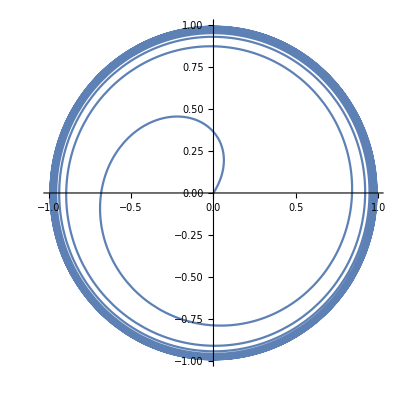

```mathematica
ParametricPlot[{(1-1/n)Cos[n], (1-1/n)Sin[n]}, {n, 1, 100}]
```

```mathematica
∫_0^7 Sin[m π x]Cos[m π x]ⅆx
```

Sin[7 m π]^2/(2 m π)

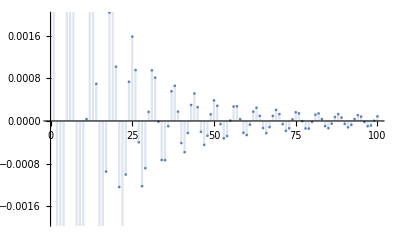

```mathematica
DiscretePlot[1/x^2 Cos[x], {x, 1, 100}]
```

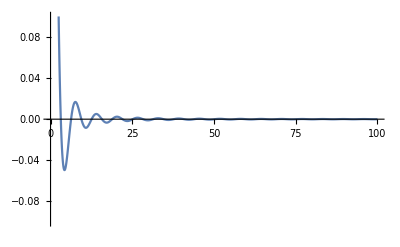

```mathematica
Plot[1/x^2 Sin[x], {x, 1, 100}, PlotRange-> {-0.1,0.1}]
```

```mathematica
Column[Union[Permutations[{a,b,c,d}, {2}]]]
```

{a,b}
{a,c}
{a,d}
{b,a}
{b,c}
{b,d}
{c,a}
{c,b}
{c,d}
{d,a}
{d,b}
{d,c}

```mathematica
Manipulate[Plot[{∑_(n=1)^100 (-1)^(n+1)/n(x-t)^n, Log[x]}, {x, -1, 3}, PlotRange-> {-2, 2}], {t, 0, 10}]
```

```mathematica
x^(2/n) == x*x^(1/n)
```

x^(2/n)==x^(1+1/n)

```mathematica
SumConvergence[(-1)^n/n, n]
```

True

```mathematica
FullSimplify[(4+2(-1)^n)^n]
```

(4+2 (-1)^n)^n

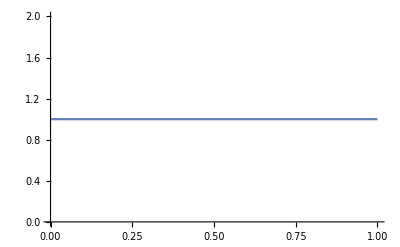

```mathematica
Plot[Limit[k^(1/n), n-> ∞], {k, 0, 1}]
```

```mathematica
Limit[(1/n)^(1/n), n-> ∞]
```

1

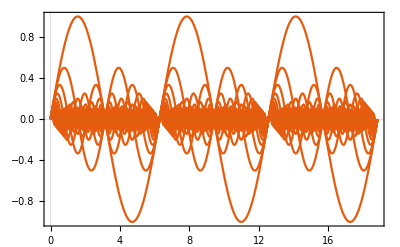

```mathematica
Plot[Table[1/n Sin[n x], {n, 1, 20}], {x, 0, 6π}, PlotRange-> {-1,1}, PlotTheme->"Scientific"]
```

```mathematica
Limit[Sin[n ], n-> ∞]
```

Indeterminate

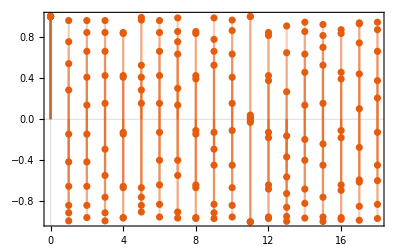

```mathematica
DiscretePlot[Table[Cos[n x], {n, 1, 10}], {x, 0, 6π}, PlotRange-> {-1,1}, PlotTheme->"Scientific"]
```

```mathematica
Limit[Table[Cos[n x], {n, 1, 10}], x-> ∞]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
Manipulate[Plot[Table[ x^n, {n, 0, t}], {x, 0, 1}, PlotTheme->"Detailed", PlotRange-> {0, 1}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[1/n Sin[n x], {n, 1, t}], {x, 0, π}, PlotTheme->"Detailed", PlotRange-> {0, 1}], {t, 1, 100, 1}]
```

```mathematica
Manipulate[Plot[Table[ {x^(1/n), x^n}, {n, 1, t}], {x, 0, 1}, PlotTheme->"Scientific", PlotRange-> {0, 1}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[ {x}, {n, 1, t}], {x, 0, 1}, PlotTheme->"Scientific", PlotRange-> {0, 1}], {t, 1, 30, 1}]
```

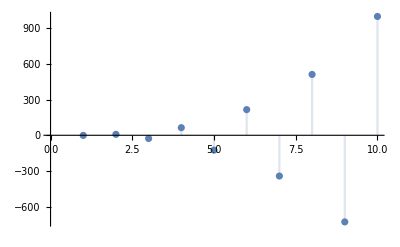

```mathematica
DiscretePlot[(-1)^n n^3, {n, 1, 10}]
```

```mathematica
Manipulate[Plot[Table[1/(n(1+x^2)), {n, 1,t}], {x, -5,5}, PlotLegends->"Expressions", PlotRange-> {0, 1}, AspectRatio->Full], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[(x^2+ n x)/n, {n, 1,t}], {x, -5,5}, PlotRange-> {-5, 5}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[(1-Abs[x])^n, {n, 1,t}], {x, -1,1}, PlotRange-> {-2, 2}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[1/n Sin[n x], {n, 1,t}], {x, -π,π}, PlotRange-> {-2, 2}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[n x^n, {n, 1,t}], {x, 0,1}, PlotRange-> {-2, 2}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[x/(1+ n x^2), {n, 1,t}], {x, -2,2}, PlotRange-> {-1, 1}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[n^2 x^n, {n, 1,t}], {x, 0,1}, PlotRange-> {-3, 3}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[(1+2 Cos[n x]^2)/(√n), {n, 1,t}], {x, π,-π}, PlotRange-> {0, 3}], {t, 1, 30, 1}]
```

```mathematica
Manipulate[Plot[Table[x/n, {n, 1,t}], {x, 0,2}, PlotRange-> {0, 1}], {t, 1, 20, 1}]
```

```mathematica
Manipulate[Plot[Table[1/(1+x^n), {n, 1,t}], {x, 0,2}, PlotRange-> {0, 1}], {t, 1, 20, 1}]
```

```mathematica
Manipulate[Plot[Table[x^n/(1+x^n), {n, 1,t}], {x, 0,2}, PlotRange-> {0, 1}], {t, 1, 20, 1}]
```

```mathematica
Manipulate[Plot[Table[x^n/(n+x^n), {n, 1,t}], {x, 0,2}, PlotRange-> {0, 1}], {t, 1, 30, 1}]
```

General::munfl: 0.0000408571^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000408571^1001 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

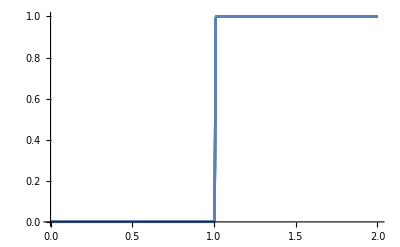

```mathematica
Plot[Table[x^n/(n+x^n), {n, 1000,1010}], {x, 0,2}, PlotRange-> {0, 1}]
```

```mathematica
Manipulate[Plot[Table[(x-1/n)^2, {n, 1,t}], {x, 0,1}, PlotRange-> {0, 1}], {t, 1, 20, 1}]
```

```mathematica
Export["/naomi/HOME/alex/Desktop/testing.gif",Table[Plot[Table[x^n/(n+x^n), {n, Max[1, t-15 ],t}], {x, 0,2}, PlotRange-> {0, 1}], {t, 1, 30, 1}], "GIF"]
```

Export::nodir: Directory /naomi/HOME/alex/Desktop/ does not exist.

Export::noopen: Cannot open /naomi/HOME/alex/Desktop/testing.gif.

$Failed